```mathematica
mat={{-Sin[theta],Cos[theta]Cos[phi],Cos[theta]Sin[phi]},
{0,-Sin[theta]Sin[phi],Sin[theta]Cos[phi]},
{Cos[theta],Sin[theta]Cos[phi],Sin[theta]Sin[phi]}};
```

```mathematica
{{-Sin[theta],Cos[theta]Cos[phi],Cos[theta]Sin[phi]},
{0,-Sin[theta]Sin[phi],Sin[theta]Cos[phi]},
{Cos[theta],Sin[theta]Cos[phi],Sin[theta]Sin[phi]}}//Det//Simplify
```

Sin[theta]

```mathematica
expr=Inverse@mat.{Sin@theta,0,1}/.{theta->θ,phi->ϕ}//FullSimplify;expr//MatrixForm
```

(1/2 (-1+2 Cos[θ]+Cos[2 θ])
(1+Cos[θ]) Cos[ϕ] Sin[θ]
(1+Cos[θ]) Sin[θ] Sin[ϕ])

```mathematica
mat={#,D[#,θ],D[#,ϕ]}&@{Cos@θ,Sin@θ Cos@ϕ,Sin@θ Sin@ϕ};mat//MatrixForm
```

(Cos[θ] | Cos[ϕ] Sin[θ] | Sin[θ] Sin[ϕ]
-Sin[θ] | Cos[θ] Cos[ϕ] | Cos[θ] Sin[ϕ]
0 | -Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ])

```mathematica
Inverse@mat//FullSimplify//MatrixForm
```

(Cos[θ] | -Sin[θ] | 0
Cos[ϕ] Sin[θ] | Cos[θ] Cos[ϕ] | -Csc[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | Cos[θ] Sin[ϕ] | Cos[ϕ] Csc[θ])

```mathematica
expr=Inverse@mat.{Cos@θ,-Sin@θ,0}//FullSimplify;expr//MatrixForm
```

(1
0
0)

## Find directions without stationary points

Start by computing derivative and imposing the discriminant to be negative. This gives a condition on the angles, which turns out to correspond to a pair of “circular” regions on the opposite sides of the sphere.

```mathematica
With[{expr=Total@Times[{a,b,c},Exp[-λ]λ^{0,1,2}/{0,1,2}!]},
ⅇ^λ D[expr,λ]//FullSimplify//Collect[#,λ,Simplify]&//Solve[#==0,λ]&
]
```

{{λ→(-b+c-√(b^2-2 a c+c^2))/c},{λ→(-b+c+√(b^2-2 a c+c^2))/c}}

```mathematica
c^2+b^2-2a c/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}//FullSimplify
```

Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])

```mathematica
Reduce[Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])<0&&0<θ<π&&0<ϕ<2π,{θ,ϕ},Reals]
```

(0<θ<2 ArcTan[1/2 (-1+√5)]&&-ArcSin[Tan[θ/2]/(-1+Tan[θ/2]^2)]<ϕ<π+ArcSin[Tan[θ/2]/(-1+Tan[θ/2]^2)])||(2 ArcTan[1/2 (1+√5)]<θ<π&&π+ArcSin[Tan[θ/2]/(-1+Tan[θ/2]^2)]<ϕ<2 π-ArcSin[Tan[θ/2]/(-1+Tan[θ/2]^2)])

```mathematica
Show[SphericalPlot3D[
If[Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])<0,1,0],
{θ,0,Pi},{ϕ,0,2Pi},PlotRange->All
],
ParametricPlot3D[
{FromSphericalCoordinates@{1,θ,-ArcSin[Cot[θ/2]]},
FromSphericalCoordinates@{1,θ,-π+ArcSin[Cot[θ/2]]}},
{θ,π/2,π},PlotRange->All]
]
```

-Graphics3D-

```mathematica
Manipulate[With[{expr=Total@Times[{Cos@θ,Sin@θ Cos@ϕ,Sin@θ Sin@ϕ},Exp[-λ]λ^{0,1,2}/{0,1,2}!]},
Plot[expr,{λ,0,10},ImageSize->Large,PlotRange->All]//Column@{#,Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])}&
],{{θ,0},0,Pi,0.01,Appearance->"Labeled"},{{ϕ,0},0,2Pi,0.01,Appearance->"Labeled"}]
```

```mathematica
Manipulate[With[{expr=Total@Times[{Cos@θ,Sin@θ Cos@ϕ,Sin@θ Sin@ϕ},Exp[-λ]λ^{0,1,2}/{0,1,2}!]},
Plot[expr,{λ,0,10},ImageSize->Large,PlotRange->All]//Column@{#,Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])}&
],{{θ,0},0,Pi,0.01,Appearance->"Labeled"},{{ϕ,0},0,2Pi,0.01,Appearance->"Labeled"}]
```

```mathematica
Simplify@D[λ ⅇ^-λ,λ]
```

-ⅇ^-λ (-1+λ)

## Stationary points in P012 space

```mathematica
f[λ_,a_,b_,c_]:=ⅇ^-λ(a+b λ+c λ^2/2);
sphericalCoordsReplRules={a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]};
fSphericalCoords[λ_,θ_,ϕ_]=f[λ,a,b,c]/.sphericalCoordsReplRules;
λpmSolutions=Solve[FullSimplify[ⅇ^λ D[f[λ,a,b,c],λ]]==0,λ]//FullSimplify[#,λ≥0]&
λpSphericalCoords[θ_,ϕ_]=FullSimplify[λpmSolutions/.sphericalCoordsReplRules]⟦2,1,2⟧;
λmSphericalCoords[θ_,ϕ_]=FullSimplify[λpmSolutions/.sphericalCoordsReplRules]⟦1,1,2⟧;
```

{{λ→-(b-c+√(b^2-2 a c+c^2))/c},{λ→(-b+c+√(b^2-2 a c+c^2))/c}}

```mathematica
FullSimplify[ⅇ^λ D[f[λ,a,b,c],λ,λ]]/.λpmSolutions⟦1⟧//FullSimplify
FullSimplify[ⅇ^λ D[f[λ,a,b,c],λ,λ]]/.λpmSolutions⟦2⟧//FullSimplify
```

√(b^2+c (-2 a+c))

-√(b^2+c (-2 a+c))

## 2D plot with different behaviours for different angles

Imposing F_max to be achieved both for a local stationary point λ and λ=∞, and using the first solution λ=λ_+ for the stationary point, we get a relation between ϕ=ϕ(θ). Actually we get two such solutions, but only one also corresponds to angles in which λ_+≥0:

```mathematica
Reduce[
Equal[(a+b λ+c λ^2/2)//.{λ->λp[a,b,c],a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]},0]&&0<θ<π&&0<ϕ<2π//FullSimplify,
{θ,ϕ}
]//FullSimplify
```

(2 θ==π&&2 ϕ==3 π)||(π/2<θ<π&&(ϕ+ArcSin[Cot[θ/2]]==2 π||π+ArcSin[Cot[θ/2]]==ϕ))

(Cot[θ/2]+√(-Cos[θ] Csc[θ/2]^2)-2 √(Cos[θ/2]^4) Csc[θ]) Tan[θ/2]

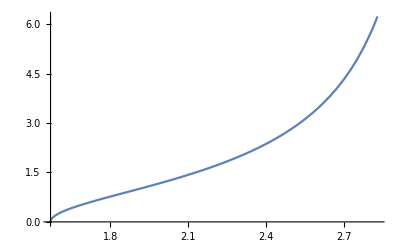

```mathematica
λp[a,b,c]/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}/.ϕ->-ArcSin[Cot[θ/2]]+2 π//FullSimplify
Plot[%,{θ,π/2,π 0.9},PlotRange->All]
```

```mathematica
λp[a,b,c]/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}/.ϕ->π+ArcSin[Cot[θ/2]]//FullSimplify
Plot[%,{θ,π/2,π}]
```

Visualise landscape of behaviour of solutions for different angles θ and ϕ

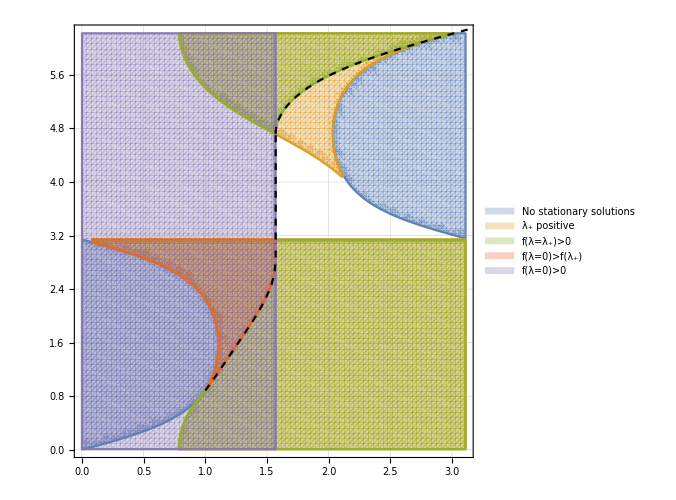

```mathematica
ClearAll[discriminantExpr,λpInSphericalCoords];
discriminantExpr[θ_,ϕ_]=Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ]);
λpInSphericalCoords[θ_,ϕ_]=λp[a,b,c]/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}//FullSimplify;
fig=Show[
RegionPlot[
{discriminantExpr[θ,ϕ]≤0,
If[discriminantExpr[θ,ϕ]>0,λpInSphericalCoords[θ,ϕ],-1]>0,
If[discriminantExpr[θ,ϕ]>0&&λpInSphericalCoords[θ,ϕ]>0,fSphericalCoords[λpInSphericalCoords[θ,ϕ],θ,ϕ],-1]>0,
θ≤π/2&&discriminantExpr[θ,ϕ]>0&&fSphericalCoords[0,θ,ϕ]>fSphericalCoords[λpInSphericalCoords[θ,ϕ],θ,ϕ],
fSphericalCoords[0,θ,ϕ]>0
},
{θ,0.001,0.99π},{ϕ,0.01,0.99 2π},PlotRangePadding->None,PlotPoints->80,
PlotLegends->{"No stationary solutions","λ_+ positive","f(λ=λ_+)>0","f(λ=0)>f(λ_+)","f(λ=0)>0"},
GridLines->Automatic,
FrameStyle->Directive[Black,Thick,Large],PlotRangePadding->None,ImageSize->500
],
ParametricPlot[
{θ,NSolve[{fSphericalCoords[0,θ,ϕ]==fSphericalCoords[λpInSphericalCoords[θ,ϕ],θ,ϕ],0<ϕ<π},ϕ,Reals]⟦1,1,2⟧},
{θ,1.,π/2},PlotStyle->Directive[Black,Thick,Dashed]
],
ParametricPlot[{π/2,ϕ},{ϕ,π,4.75},PlotStyle->Directive[Black,Thick,Dashed]],
ParametricPlot[{θ,2π-ArcSin@Cot[θ/2]},{θ,π/2,π},PlotStyle->Directive[Black,Thick,Dashed]]
(*Graphics[{PointSize@0.015,Dynamic@Point@movingPoint}]*)
]//Quiet
```

```mathematica
exportHere["P012_linearfunctional_landscape.pdf",fig]
```

/home/lk/Documents/docs/research/Radim/Mathematica/P012_linearfunctional_landscape.pdf

```mathematica
SystemOpen@NotebookDirectory[]
```

```mathematica
Manipulate[
movingPoint={θ,ϕ};
Plot[fSphericalCoords[λ,θ,ϕ],{λ,0,10},Epilog->{Red,InfiniteLine@{{#,0},{#,1}}&@λpSphericalCoords[θ,ϕ]}],
{{θ,2.5},0,π,Appearance->"Labeled"},
{{ϕ,3.5},0,2π,Appearance->"Labeled"},ControlPlacement->Right
]
```

Looking for the angles corresponding to the “K∞” sector of the boundary

```mathematica
Equal[ⅇ^-λ(a+b λ+c λ^2/2)-a//.{λ->λp[a,b,c],a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]},0]&&0<θ<π&&0<ϕ<2π//FullSimplify
```

ⅇ^Cot[ϕ] Sin[θ] Sin[ϕ]+ⅇ^Cot[ϕ] √Sin[θ] √(Sin[θ]-2 Cos[θ] Sin[ϕ])==ⅇ^(1+(Csc[ϕ] √(Sin[θ]-2 Cos[θ] Sin[ϕ]))/(√Sin[θ])) Cos[θ]&&0<θ<π&&0<ϕ<2 π

Find manually the set of pairs (θ,ϕ) for which the maximum is obtained both for λ_+ and for λ=0

```mathematica
Table[{θ0,#}&/@NSolve[{FullSimplify[ⅇ^Cot[ϕ] Sin[θ] Sin[ϕ]+ⅇ^Cot[ϕ] √Sin[θ] √(Sin[θ]-2 Cos[θ] Sin[ϕ])-ⅇ^(1+(Csc[ϕ] √(Sin[θ]-2 Cos[θ] Sin[ϕ]))/(√Sin[θ])) Cos[θ]/.θ->θ0]==0,0≤ϕ≤2π},ϕ,Reals]⟦All,1,2⟧//Apply@Sequence,
{θ0,π/2,π,0.1}]~Monitor~θ0
```

{{1.5708,3.08664},{1.5708,4.71239},{1.6708,4.61189},{1.6708,4.61189},{1.7708,4.50826},{1.8708,4.39789},{1.9708,4.27586},{2.0708,4.13445},{2.0708,4.13445},{2.1708,3.95897},{2.1708,3.95897},{2.2708,3.7693},{2.3708,3.63207},{2.4708,3.53156},{2.5708,3.45334},{2.6708,3.38842},{2.7708,3.33128},{2.8708,3.27834},{2.9708,3.2273},{3.0708,3.17701}}

```mathematica
planeExpr[θ_]=a p0+b p1+c p2/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}/.ϕ->-ArcSin[Cot[θ/2]]+2 π//FullSimplify;
Manipulate[
Show[ContourPlot3D[
p1^2==2 p0 p2,
{p0,0,1},{p1,0,1},{p2,0,1},
PlotRange->All,PlotPoints->40,AxesLabel->{0,1,2},ContourStyle->Directive[Green,Opacity@0.5]
],
ParametricPlot3D[Exp[-λ]λ^{0,1,2}/{0,1,2}!,{λ,0,10},PlotStyle->Red],
ContourPlot3D[planeExpr[θ]==const,{p0,0,1},{p1,0,1},{p2,0,1}]
],
{{θ,π/2+0.01},π/2+0.01,π,0.01,Appearance->"Labeled"},
{{const,0},0,1,0.01,Appearance->"Labeled"},ControlPlacement->Right
]
```

## Explore directions with stationary points

First of all we need to figure out the regions in which the two solutions are positive, and therefore viable

```mathematica
With[{expr=Total@Times[{a,b,c},Exp[-λ]λ^{0,1,2}/{0,1,2}!]},
ⅇ^λ D[expr,λ]//FullSimplify//Collect[#,λ,Simplify]&//Solve[#==0,λ]&
]/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}//Map@FullSimplify
%⟦All,1,2⟧//Map[Reduce[#≥0&&0<θ<π&&0<ϕ<2π,{θ,ϕ},Reals]&]
```

{{λ→1-Cot[ϕ]-Csc[θ] Csc[ϕ] √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2)},{λ→1-Cot[ϕ]+Csc[θ] Csc[ϕ] √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2)}}

```mathematica
b^2-2 a c+c^2/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}//FullSimplify
```

Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])

```mathematica
expr=ReplaceAll[Total@Times[{a,b,c},Exp[-λ]λ^{0,1,2}/{0,1,2}!],λ->(-b+c+√(b^2-2 a c+c^2))/c]//FullSimplify
```

(c+√(b^2-2 a c+c^2)) ⅇ^(-(-b+c+√(b^2-2 a c+c^2))/c)

```mathematica
simplifiedExpr=ReplaceRepeated[{expr,D[expr,a],D[expr,b]}//FullSimplify,{(-b+c+√(b^2-2 a c+c^2))/c->Subscript[C, 1]}]
```

{(c+√(b^2-2 a c+c^2)) ⅇ^-C_1,ⅇ^-C_1,ⅇ^-C_1 C_1}

```mathematica
matCartesianCoords={#,D[#,a],D[#,b]}&@{a,b,Sqrt[1-a^2-b^2]};matCartesianCoords//MatrixForm;
matCartesianCoordsInv=Inverse@matCartesianCoords//Simplify;matCartesianCoordsInv//MatrixForm
```

(a | 1-a^2 | -a b
b | -a b | 1-b^2
√(1-a^2-b^2) | -a √(1-a^2-b^2) | -b √(1-a^2-b^2))

```mathematica
matCartesianCoordsInv.simplifiedExpr/.Subscript[C, 1]->(-b+c+√(b^2-2 a c+c^2))/c//FullSimplify
```

{((c+a (b^2-b (c+√(b^2-2 a c+c^2))+c (-a+c+√(b^2-2 a c+c^2)))) ⅇ^(-(-b+c+√(b^2-2 a c+c^2))/c))/c,((c+√(b^2-2 a c+c^2)+b (-1+b^2-b (c+√(b^2-2 a c+c^2))+c (-a+c+√(b^2-2 a c+c^2)))) ⅇ^(-(-b+c+√(b^2-2 a c+c^2))/c))/c,(√(1-a^2-b^2) (b^2-b (c+√(b^2-2 a c+c^2))+c (-a+c+√(b^2-2 a c+c^2))) ⅇ^(-(-b+c+√(b^2-2 a c+c^2))/c))/c}

```mathematica
2%54⟦1⟧%54⟦3⟧//FullSimplify
```

1/c^2 2 √(1-a^2-b^2) (b^2-b (c+√(b^2-2 a c+c^2))+c (-a+c+√(b^2-2 a c+c^2))) (c+a (b^2-b (c+√(b^2-2 a c+c^2))+c (-a+c+√(b^2-2 a c+c^2)))) ⅇ^(-(2 (-b+c+√(b^2-2 a c+c^2)))/c)

```mathematica
%54⟦2⟧//FullSimplify
```

((c+√(b^2-2 a c+c^2)+b (-1+b^2-b (c+√(b^2-2 a c+c^2))+c (-a+c+√(b^2-2 a c+c^2)))) ⅇ^(-(-b+c+√(b^2-2 a c+c^2))/c))/c

```mathematica
expr=ReplaceAll[Total@Times[{a,b,c},Exp[-λ]λ^{0,1,2}/{0,1,2}!],λ->(-b+c+√(b^2-2 a c+c^2))/c]/.{a->Cos[θ],b->Sin[θ]Cos[ϕ],c->Sin[θ]Sin[ϕ]}//FullSimplify
```

ⅇ^(-1+Cot[ϕ]-Csc[θ] Csc[ϕ] √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2)) (Sin[θ] Sin[ϕ]+√(Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])))

```mathematica
mat={#,D[#,θ],D[#,ϕ]}&@{Cos@θ,Sin@θ Cos@ϕ,Sin@θ Sin@ϕ};mat//MatrixForm;
Inverse@mat//Simplify//MatrixForm
```

(Cos[θ] | -Sin[θ] | 0
Cos[ϕ] Sin[θ] | Cos[θ] Cos[ϕ] | -Csc[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | Cos[θ] Sin[ϕ] | Cos[ϕ] Csc[θ])

```mathematica
{{a,b,c},{1,Subscript[b, a],0},{0,Subscript[b, c],1}}//Inverse//Simplify//MatrixForm
```

(b_a/(-b+a b_a+c b_c) | (b-c b_c)/(b-a b_a-c b_c) | (c b_a)/(b-a b_a-c b_c)
1/(b-a b_a-c b_c) | a/(-b+a b_a+c b_c) | c/(-b+a b_a+c b_c)
b_c/(-b+a b_a+c b_c) | (a b_c)/(b-a b_a-c b_c) | (b-a b_a)/(b-a b_a-c b_c))

```mathematica
sol[θ_,ϕ_]=Dot[Simplify@Inverse@mat,{expr,D[expr,θ],D[expr,ϕ]}]//FullSimplify[#,0≤θ≤π&&0≤ϕ≤2π]&;
```

```mathematica
sol[θ,ϕ]/.{1-2Cot@θ Sin@ϕ->Subscript[C, 1],Sin[θ]^2-Sin[2θ]Sin@ϕ->Subscript[C, 2]}//FullSimplify[#,0≤θ≤π&&0≤ϕ≤2π]&//MatrixForm
```

(ⅇ^(-1+Cot[ϕ]-Csc[ϕ] √C_1)
ⅇ^(-1+Cot[ϕ]-Csc[ϕ] √C_1) (1-Cot[ϕ]+Csc[θ] Csc[ϕ] √C_2)
(ⅇ^(-1+Cot[ϕ]-Csc[ϕ] √C_1) (2 Cot[θ]-Csc[ϕ]) (Cos[θ]+(Cos[ϕ]-Csc[ϕ]) Sin[θ]+(-1+Cot[ϕ]) √C_2))/(√(Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])) √C_1))

```mathematica
ParametricPlot3D[If[Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])≥0,Chop@sol[θ,ϕ]],{θ,0,π},{ϕ,.001,2π},PlotRange->ConstantArray[{0,1},3]]
```

General::munfl: Exp[-1596.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
Plot3D[If[Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])>0,expr],{θ,0.01,π},{ϕ,0.01,2π}]
```

General::munfl: Exp[-887.634] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
D[expr,θ]//FullSimplify
D[expr,ϕ]//FullSimplify
```

(Csc[θ] (-2+Sin[2 θ] Sin[ϕ]+2 Cos[θ] √(Sin[θ]^2-Sin[2 θ] Sin[ϕ])) (Cosh[Cot[ϕ]-Csc[θ] Csc[ϕ] √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2)]+Sinh[Cot[ϕ]-Csc[θ] Csc[ϕ] √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2)]))/(2 ⅇ)

-(ⅇ^(-1+Cot[ϕ]-Csc[θ] Csc[ϕ] √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2)) Csc[ϕ] Sin[θ] √(Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])) (4-5 Cot[ϕ]+4 Cos[ϕ] (Cot[θ]-Csc[θ] √(Sin[θ]^2-Sin[2 θ] Sin[ϕ]))+Csc[ϕ] (Cos[3 ϕ]+4 Csc[θ] √(Sin[θ]^2-Sin[2 θ] Sin[ϕ]))))/(4 √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2))

```mathematica
With[{expr=Total@Times[{a,b,c},Exp[-λ]λ^{0,1,2}/{0,1,2}!]},
ⅇ^λ D[expr,λ]//FullSimplify//Collect[#,λ,Simplify]&//Solve[#==0,λ]&
]⟦1,1,2⟧//Reduce[#≥0&&b^2-2a c+c^2≥0,{a,b,c}]&//FullSimplify
```

(a<0&&((b≤a&&c≠0)||(a<b≤0&&√(a^2-b^2)+c≤a)||(0<b<-a&&(√(a^2-b^2)+c≤a||a+√(a^2-b^2)≤c<0))||(a+b≥0&&c<0)))||(a==0&&(c<0||(c>0&&b≤0)))||(a>0&&((a==b&&(c<0||√(a^2-b^2)+c≥a))||(c≠0&&a+b≤0)||((c<0||c≥a+√(a^2-b^2))&&(0≤b<a||(a+b>0&&b<0)))||(b<0&&a+b>0&&c>0&&√(a^2-b^2)+c≤a)||(c<0&&b>a)))

```mathematica
SphericalPlot3D[
If[
(*Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])<0,1,*)
Sin[θ] (Sin[θ]-2 Cos[θ] Sin[ϕ])>0&&1-Cot[ϕ]-Csc[θ] Csc[ϕ] √((1+Cot[ϕ]^2-2 Cot[θ] Csc[ϕ]) Sin[θ]^2 Sin[ϕ]^2)>0,1,0
],
{θ,0,Pi},{ϕ,0,2Pi},PlotPoints->40,MaxRecursion->3
]
```

-Graphics3D-